```mathematica
filesAR=FileNames["/home/carla/GDC/DLB/GDC_Conf_AR_DLB_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla/GDC/DLB/GDC_Conf_BR_DLB_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]]
```

{{{1.,1,1},{1.,1.,0.00014928},{1,1.,1.50788×10^-6,0.00014928}},{{1.,1,1},{1.,1.,0.000199089},{1,1.,4.87964×10^-9,0.000199089}},{{0.000765111,1,1307},{0.000635999,0.000765111,0.000129194},{0.711231,0.000765111,1.2268×10^-6,0.000129194}},{{0.00609756,1,164},{0.00597582,0.00609756,0.000122473},{0.960851,0.00609756,8.87012×10^-8,0.000122473}},{{0.00714286,5,700},{0.0069381,0.00714286,0.000206186},{0.944266,0.00714286,1.34005×10^-9,0.000206186}},{{0.00390625,5,1280},{0.00385097,0.00390625,0.0000554912},{0.972093,0.00390625,2.94314×10^-11,0.0000554912}},{{0.0223325,9,403},{0.0222051,0.0223325,0.000130351},{0.98865,0.0223325,1.18417×10^-14,0.000130351}},{{0.025641,9,351},{0.0255134,0.025641,0.000130951},{0.990096,0.025641,1.60368×10^-15,0.000130951}},{{1.,1,1},{1.,1.,0.0000130309},{1,1.,2.16208×10^-18,0.0000130309}}}

```mathematica
confBR=dataBR[[All,1]]
```

{{{1.,160,160},{1.,1.,0.000199089},{1,1.,7.80743×10^-7,0.000199089}},{{1.,7,7},{1.,1.,0.000129194},{1,1.,6.57045×10^-9,0.000129194}},{{0.000765111,1,1307},{0.000642717,0.000765111,0.000122473},{0.724184,0.000765111,7.06905×10^-7,0.000122473}},{{0.00609756,305,50020},{0.00596974,0.00609756,0.000128589},{0.958935,0.00609756,9.57564×10^-8,0.000128589}},{{0.00397649,138,34704},{0.00392121,0.00397649,0.0000554912},{0.972581,0.00397649,7.97959×10^-10,0.0000554912}},{{0.000824742,2350,2849375},{0.000817805,0.000824742,6.94245×10^-6},{0.983319,0.000824742,8.37255×10^-11,6.94245×10^-6}},{{0.00618132,9,1456},{0.00605116,0.00618132,0.000130951},{0.958755,0.00618132,6.6523×10^-15,0.000130951}},{{0.025641,36,1404},{0.0255135,0.025641,0.000130821},{0.990105,0.025641,3.03556×10^-15,0.000130821}}}

```mathematica
dojAR=confAR[[All,1]][[All,1]]
zAR=confAR[[All,2]][[All,1]]
fAR=confAR[[All,3]][[All,1]]
```

{1.,1.,0.000765111,0.00609756,0.00714286,0.00390625,0.0223325,0.025641,1.}

{1.,1.,0.000635999,0.00597582,0.0069381,0.00385097,0.0222051,0.0255134,1.}

{1,1,0.711231,0.960851,0.944266,0.972093,0.98865,0.990096,1}

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{1.,1.,0.000765111,0.00609756,0.00397649,0.000824742,0.00618132,0.025641}

{1.,1.,0.000642717,0.00596974,0.00392121,0.000817805,0.00605116,0.0255135}

{1,1,0.724184,0.958935,0.972581,0.983319,0.958755,0.990105}

```mathematica
(*sList={"S0","S1","S2","S3","S4","S5","S6","S7","S8"};
dojP=Labeled[#[[1]],#[[2]]]&/@Map[{doj[[#]],sList[[#]]}&,ran]*)

sList={0,1,2,3,4,5,6,7,8};
sList2={0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];


dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&,ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&,ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&,ran2];
```

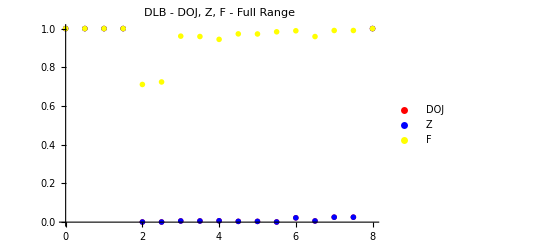

```mathematica
PlotAllParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"DLB - DOJ, Z, F - Full Range", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

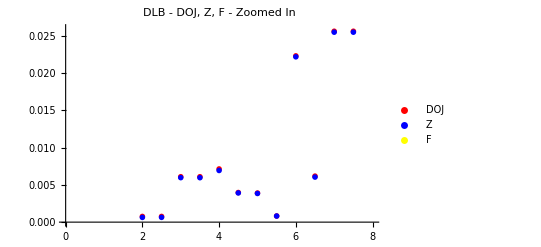

```mathematica
PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.026},  PlotLabel->"DLB - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla/GDC/DLB/"];
(*Put[{confM,{bvE,bvHEK}},filenameOut]*)
Put[Union[dojPAR,dojPBR],"DLB_DOJ.txt"]
Put[Union[zPAR,zPBR],"DLB_Z.txt"]
Put[Union[fPAR,fPBR],"DLB_F.txt"]
Export["DLB_ALL.jpeg",PlotAllParts,ImageSize->850]
Export["DLB_Zoomed_In.jpeg",PlotParts,ImageSize->850]
```

DLB_ALL.jpeg

DLB_Zoomed_In.jpeg